#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documents/Collaborations/En progreso/2022-06-INAOE-CSM/6-Dimero

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
graphsOptsDensityExport :={PlotLegends->None,FrameTicks->None, BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> False, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None}
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Near Field Abs

```mathematica
cases = {1,2};
radius = 7.30;
ha = 0. * radius
```

0.

```mathematica
data = FileNames["*EDimmer-Total*csv"]
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
limData = radius*4.5;
lim = radius*4;
```

{EDimmer-Total-04.csv,EDimmer-Total-14.csv}

EDimmer-Total-04.csv
EDimmer-Total-14.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,2]; (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {y, #2 * -z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataX]}];
```

8.4109

{{GrayLevel[1],Dashing[{Small,Small}],Line[{{-29.2,0},{29.2,0}}],GrayLevel[0],Circle[{-9.3,0},7.3],Circle[{9.3,0},7.3]},{GrayLevel[1],Dashing[{Small,Small}],Line[{{-29.2,0},{29.2,0}}],GrayLevel[0],Circle[{-14.3,0},7.3],Circle[{14.3,0},7.3]}}

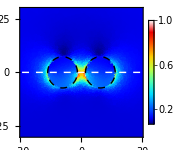
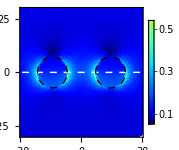

```mathematica
case = Table[i,{i,{2,7}}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{-1*radius-#,0},radius],Circle[{+1*radius+#,0},radius]}&/@case

plotsX = MapThread[ListDensityPlot[#1,
            PlotRange->{{-1,1},{-1,1},{-1,2}}*lim,
            ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
```

{{GrayLevel[1],Dashing[{Small,Small}],Line[{{-29.2,0},{29.2,0}}],GrayLevel[0],Circle[{-9.3,0},7.3],Circle[{9.3,0},7.3]},{GrayLevel[1],Dashing[{Small,Small}],Line[{{-29.2,0},{29.2,0}}],GrayLevel[0],Circle[{-14.3,0},7.3],Circle[{14.3,0},7.3]}}

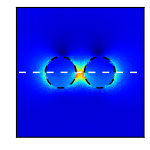
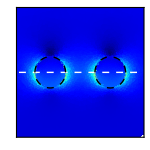

```mathematica
case = Table[i,{i,{2,7}}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{-1*radius-#,0},radius],Circle[{+1*radius+#,0},radius]}&/@case

plotsX = MapThread[ListDensityPlot[#1,
            PlotRange->{{-1,1},{-1,1},{-1,2}}*lim,
            ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
```

-Graphics-

-Graphics-

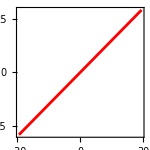

```mathematica
legends = {0,0,0};
legends[[1]] = Plot[x, {x, 0, max}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {Automatic, None}},
  FrameStyle -> Black,    Frame-> True,
  AspectRatio -> 1/30, 
  PlotRange -> All, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
 
legends[[2]] =  DensityPlot[x, {x, 0,max}, {y, 0, 1}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 1/30, 
  PlotRange -> All, ColorFunction -> JetExtended, 
  PlotPoints -> 40, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
 
legends[[3]] = Plot[x, {x, -lim,lim}, BaseStyle -> texStyle, 
  FrameTicks -> Automatic,
  FrameStyle -> Black,    Frame-> True,
  AspectRatio -> 1, 
  PlotStyle->Red,
  PlotRange -> All, PlotRangePadding -> None, 
PlotRange -> Full, ImageSize -> 150]
```

```mathematica
name = "2-NearY"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plotsY]
MapIndexed[Export[FileNameJoin[{"Normal",name,"Legend"<>ToString[First[#2]]<>{".pdf",".svg",".pdf"}[[First[#2]]]}],#1]&,legends]
name = "2-NearX"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plotsX]
```

2-NearY

plotsY

{Normal/2-NearY/Legend1.pdf,Normal/2-NearY/Legend2.svg,Normal/2-NearY/Legend3.pdf}

2-NearX

{Normal/2-NearX/2-NearX1.svg,Normal/2-NearX/2-NearX2.svg}